```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/StocForm_for_Gauge/num"];
```

```mathematica
SgE=(e^3 B0)/(6 π^2)(E0^2/(E0^2+B0^2)Coth[π B0/E0]);
SgEp=(e^3 B0)/(12 π^2)(B0^2/(E0^2+B0^2)Coth[π B0/E0]+π B0/E0 Csch[π B0/E0]^2);
SgB=(e^3 E0)/(6 π^2)(B0^2/(E0^2+B0^2)Coth[π B0/E0]);
SgBp=(e^3 E0)/(12 π^2)(E0^2/(E0^2+B0^2)Coth[π B0/E0]-π B0/E0 Csch[π B0/E0]^2);
```

```mathematica
Limit[Coth[x],{x->∞}]
```

1

```mathematica
SgE/.{B0->10^3 E0}//N
SgEp/.{B0->10^3 E0}//N
```

0.0000168868 e^3 E0

General::munfl: Csch[3141.59] is too small to represent as a normalized machine number; precision may be lost.

8.44342 e^3 E0

```mathematica
SgB/.{B0->10E0}//N
SgBp/.{B0->10E0}//N
```

0.0167197 e^3 E0

0.0000835983 e^3 E0

```mathematica
2xi-1.2xi/.{xi->7}
```

5.6

```mathematica
E0sol[x_]=E0/.Solve[SgB+SgBp==2xi(*-xi/2*)/.{B0->x E0},E0][[1]]
```

(48 π^2 (xi+x^2 xi) Sinh[π x]^2)/(e^3 (-2 π x-2 π x^3+Sinh[2 π x]+2 x^2 Sinh[2 π x]))

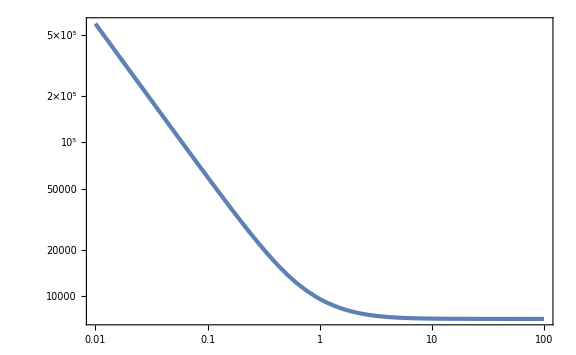

```mathematica
LogLogPlot[E0sol[x]/.{xi->10,e->0.55},{x,0.01,100}]
```

```mathematica
Limit[E0sol[x],{x->∞}]
```

(12 π^2 xi)/e^3

```mathematica
W[z_,xi_]=WhittakerW[-I xi,1/2,-2I z];
Wp[z_,xi_]=D[W[z,xi], z]//Simplify
WS[z_,xe_,Sigma_]=WhittakerW[-I xe,(1+Sigma)/2,-2I z]//Simplify
WSp[z_,xe_,Sigma_]=D[WS[z,xe,Sigma], z]//Simplify
MS[z_,xe_,Sigma_]=WhittakerM[-I xe,(1+Sigma)/2,-2I z]//Simplify
MSp[z_,xe_,Sigma_]=D[MS[z,xe,Sigma], z]//Simplify
```

(-WhittakerW[1-ⅈ xi,1/2,-2 ⅈ z]+ⅈ (xi-z) WhittakerW[-ⅈ xi,1/2,-2 ⅈ z])/z

WhittakerW[-ⅈ xe,(1+Sigma)/2,-2 ⅈ z]

(-WhittakerW[1-ⅈ xe,(1+Sigma)/2,-2 ⅈ z]+ⅈ (xe-z) WhittakerW[-ⅈ xe,(1+Sigma)/2,-2 ⅈ z])/z

WhittakerM[-ⅈ xe,(1+Sigma)/2,-2 ⅈ z]

((2+Sigma-2 ⅈ xe) WhittakerM[1-ⅈ xe,(1+Sigma)/2,-2 ⅈ z]+2 ⅈ (xe-z) WhittakerM[-ⅈ xe,(1+Sigma)/2,-2 ⅈ z])/(2 z)

### gamma = 2xieff

```mathematica
c1[xi_,xe_,Sigma_]=γ^(-Sigma/2)Gamma[1+I xe+Sigma/2]/(2I Gamma[Sigma+2])(Wp[γ,xi]MS[γ,xe,Sigma]-W[γ,xi]MSp[γ,xe,Sigma]-Sigma/(2γ)W[γ,xi]MS[γ,xe,Sigma])/.{γ->2xe}//Simplify;
c2[xi_,xe_,Sigma_]=-γ^(-Sigma/2)Gamma[1+I xe+Sigma/2]/(2I Gamma[Sigma+2])(Wp[γ,xi]WS[γ,xe,Sigma]-W[γ,xi]WSp[γ,xe,Sigma]-Sigma/(2γ)W[γ,xi]WS[γ,xe,Sigma])/.{γ->2xe}//Simplify;
```

```mathematica
Clear[PBBoH4,PEEoH4]
```

```mathematica
PBBoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^(4+Sigma)Abs[c1[xi,xe,Sigma]WS[z,xe,Sigma]+c2[xi,xe,Sigma]MS[z,xe,Sigma]]^2/;z<2xe
PBBoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^4 Abs[W[z,xi]]^2/;!(z<2xe)
PEEoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^(4+Sigma)Abs[c1[xi,xe,Sigma]WSp[z,xe,Sigma]+c2[xi,xe,Sigma]MSp[z,xe,Sigma]+Sigma/(2z)(c1[xi,xe,Sigma]WS[z,xe,Sigma]+c2[xi,xe,Sigma]MS[z,xe,Sigma])]^2/;z<2xe
PEEoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^4 Abs[Wp[z,xi]^2]/;!(z<2xe)
```

```mathematica
N[PBBoH4[1,5+1/2,5,4],30]
```

7973.61558354558003050130794792

```mathematica
ListPBBxp1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEExp1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx2=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,2,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx2=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,2,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx5=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,5,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx5=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,5,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx10=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,10,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx10=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,10,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{2.95361,Null}

{4.064,Null}

{2.79609,Null}

{5.24741,Null}

{2.26155,Null}

{5.70716,Null}

{2.88511,Null}

{7.71716,Null}

{2.61509,Null}

{8.52234,Null}

```mathematica
ListPBBSp1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,0.1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEESp1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,0.1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS2=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,2],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES2=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,2],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS5=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,5],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES5=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,5],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS10=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES10=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{2.31114,Null}

{6.0984,Null}

{1.90831,Null}

{5.67903,Null}

{2.24124,Null}

{2.86161,Null}

{2.17093,Null}

{4.95978,Null}

{2.17984,Null}

{5.21927,Null}

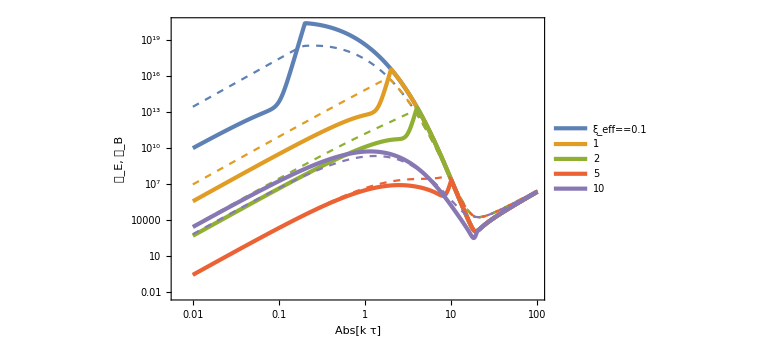

```mathematica
ListLogLogPlot[{ListPEExp1,ListPBBxp1,ListPEEx1,ListPBBx1,ListPEEx2,ListPBBx2,ListPEEx5,ListPBBx5,ListPEEx10,ListPBBx10},PlotStyle->{{AbsoluteThickness[3],Color[1]},{Dashed,Color[1]},{AbsoluteThickness[3],Color[2]},{Dashed,Color[2]},{AbsoluteThickness[3],Color[3]},{Dashed,Color[3]},{AbsoluteThickness[3],Color[4]},{Dashed,Color[4]},{AbsoluteThickness[3],Color[5]},{Dashed,Color[5]}},PlotLegends->Placed[LineLegend[{Subscript[ξ, eff]==0.1,None,1,None,2,None,5,None,10},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.7}],FrameLabel->{{Row[{Subscript[𝒫, "E"],", ",Subscript[𝒫, B]}],None},{Abs[k τ],Row[{ξ==10,", ",Σ==10}]}}]
```

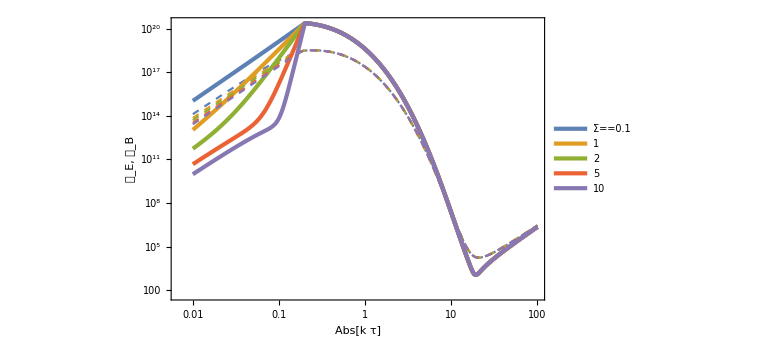

```mathematica
ListLogLogPlot[{ListPEESp1,ListPBBSp1,ListPEES1,ListPBBS1,ListPEES2,ListPBBS2,ListPEES5,ListPBBS5,ListPEES10,ListPBBS10},PlotStyle->{{AbsoluteThickness[3],Color[1]},{Dashed,Color[1]},{AbsoluteThickness[3],Color[2]},{Dashed,Color[2]},{AbsoluteThickness[3],Color[3]},{Dashed,Color[3]},{AbsoluteThickness[3],Color[4]},{Dashed,Color[4]},{AbsoluteThickness[3],Color[5]},{Dashed,Color[5]}},PlotLegends->Placed[LineLegend[{Σ==0.1,None,1,None,2,None,5,None,10},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.7}],FrameLabel->{{Row[{Subscript[𝒫, "E"],", ",Subscript[𝒫, B]}],None},{Abs[k τ],Row[{ξ==10,", ",Subscript[ξ, eff]==0.1}]}}]
```

### gamma = 2xi

```mathematica
c1[xi_,xe_,Sigma_]=γ^(-Sigma/2)Gamma[1+I xe+Sigma/2]/(2I Gamma[Sigma+2])(Wp[γ,xi]MS[γ,xe,Sigma]-W[γ,xi]MSp[γ,xe,Sigma]-Sigma/(2γ)W[γ,xi]MS[γ,xe,Sigma])/.{γ->2xi}//Simplify;
c2[xi_,xe_,Sigma_]=-γ^(-Sigma/2)Gamma[1+I xe+Sigma/2]/(2I Gamma[Sigma+2])(Wp[γ,xi]WS[γ,xe,Sigma]-W[γ,xi]WSp[γ,xe,Sigma]-Sigma/(2γ)W[γ,xi]WS[γ,xe,Sigma])/.{γ->2xi}//Simplify;
```

```mathematica
Clear[PBBoH4,PEEoH4]
```

```mathematica
PBBoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^(4+Sigma)Abs[c1[xi,xe,Sigma]WS[z,xe,Sigma]+c2[xi,xe,Sigma]MS[z,xe,Sigma]]^2/;z<2xi
PBBoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^4 Abs[W[z,xi]]^2/;!(z<2xi)
PEEoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^(4+Sigma)Abs[c1[xi,xe,Sigma]WSp[z,xe,Sigma]+c2[xi,xe,Sigma]MSp[z,xe,Sigma]+Sigma/(2z)(c1[xi,xe,Sigma]WS[z,xe,Sigma]+c2[xi,xe,Sigma]MS[z,xe,Sigma])]^2/;z<2xi
PEEoH4[z_,xi_,xe_,Sigma_]:=1/(4 π^2)E^(π xi)z^4 Abs[Wp[z,xi]^2]/;!(z<2xi)
```

```mathematica
N[PBBoH4[1,5+1/2,5,4],30]
```

4955.27782131228327958640544442

```mathematica
ListPBBxp1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEExp1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx2=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,2,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx2=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,2,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx5=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,5,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx5=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,5,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBx10=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,10,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx10=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,10,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{2.15494,Null}

{5.08962,Null}

{1.87407,Null}

{7.34875,Null}

{2.32208,Null}

{6.31485,Null}

{2.47044,Null}

{7.72673,Null}

{2.24511,Null}

{7.81454,Null}

```mathematica
ListPBBSp1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,0.1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEESp1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,0.1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS1=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES1=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,1],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS2=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,2],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES2=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,2],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS5=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,5],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES5=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,5],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPBBS10=ParallelTable[{10^logz,N[PBBoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEES10=ParallelTable[{10^logz,N[PEEoH4[10^logz,10,0.1,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{2.7992,Null}

{4.47919,Null}

{2.12599,Null}

{5.27462,Null}

{2.52994,Null}

{4.32248,Null}

{2.14838,Null}

{3.60828,Null}

{2.25366,Null}

{4.05925,Null}

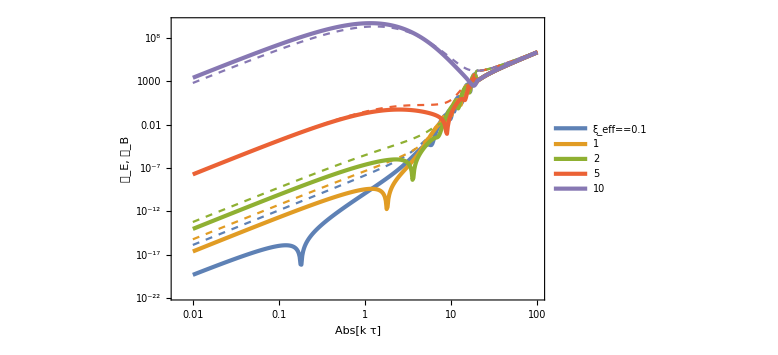

```mathematica
ListLogLogPlot[{ListPEExp1,ListPBBxp1,ListPEEx1,ListPBBx1,ListPEEx2,ListPBBx2,ListPEEx5,ListPBBx5,ListPEEx10,ListPBBx10},PlotStyle->{{AbsoluteThickness[3],Color[1]},{Dashed,Color[1]},{AbsoluteThickness[3],Color[2]},{Dashed,Color[2]},{AbsoluteThickness[3],Color[3]},{Dashed,Color[3]},{AbsoluteThickness[3],Color[4]},{Dashed,Color[4]},{AbsoluteThickness[3],Color[5]},{Dashed,Color[5]}},PlotLegends->Placed[LineLegend[{Subscript[ξ, eff]==0.1,None,1,None,2,None,5,None,10},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.3}],FrameLabel->{{Row[{Subscript[𝒫, "E"],", ",Subscript[𝒫, B]}],None},{Abs[k τ],Row[{ξ==10,", ",Σ==10, ", ", γ==2ξ}]}}]
```

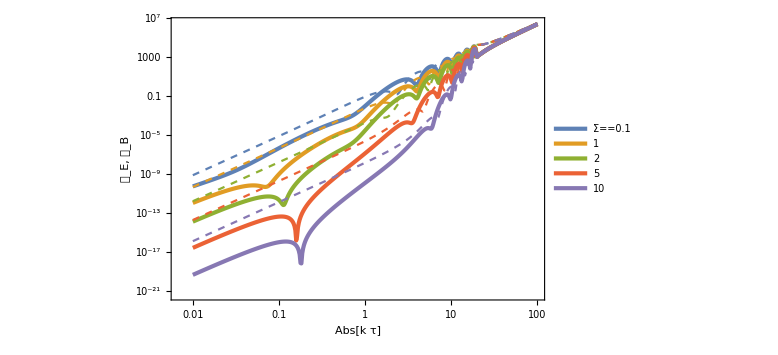

```mathematica
ListLogLogPlot[{ListPEESp1,ListPBBSp1,ListPEES1,ListPBBS1,ListPEES2,ListPBBS2,ListPEES5,ListPBBS5,ListPEES10,ListPBBS10},PlotStyle->{{AbsoluteThickness[3],Color[1]},{Dashed,Color[1]},{AbsoluteThickness[3],Color[2]},{Dashed,Color[2]},{AbsoluteThickness[3],Color[3]},{Dashed,Color[3]},{AbsoluteThickness[3],Color[4]},{Dashed,Color[4]},{AbsoluteThickness[3],Color[5]},{Dashed,Color[5]}},PlotLegends->Placed[LineLegend[{Σ==0.1,None,1,None,2,None,5,None,10},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.85,0.3}],FrameLabel->{{Row[{Subscript[𝒫, "E"],", ",Subscript[𝒫, B]}],None},{Abs[k τ],Row[{ξ==10,", ",Subscript[ξ, eff]==0.1, ", ",γ==2ξ}]}}]
```

```mathematica
ListPBBx25=ParallelTable[{10^logz,N[PBBoH4[10^logz,25,20,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
ListPEEx25=ParallelTable[{10^logz,N[PEEoH4[10^logz,25,20,10],30]},{logz,-2,2,1/100}];//AbsoluteTiming
```

{4.73191,Null}

{12.0906,Null}

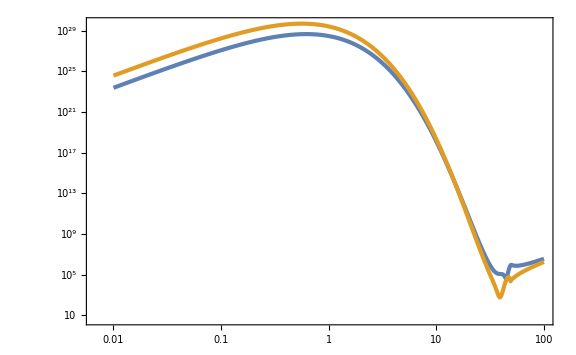

```mathematica
ListLogLogPlot[{ListPBBx25,ListPEEx25}]
```

```mathematica
consistentList=Sort[Import["c++/consistentEB.dat"]]
```

{{1,0.312567,0.5282,0.000384907,0.00054997,0.000650445,0.000113658},{1.5,0.998636,1.41866,0.00132098,0.00133767,0.00187659,0.000461609},{2,3.17476,3.17214,0.0044766,0.00234003,0.00447291,0.00213463},{2.5,10.5913,7.02783,0.0141397,0.0044262,0.00938237,0.00867526},{3,35.6798,16.9603,0.0429988,0.0128218,0.0204393,0.0284751},{3.5,109.519,42.7182,0.12383,0.0397951,0.0483003,0.0808607},{4,269.708,97.5177,0.298027,0.0992801,0.107757,0.191428},{4.5,518.653,187.548,0.573129,0.190913,0.207247,0.368141},{5,831.904,310.67,0.928166,0.304434,0.346618,0.600814},{5.5,1189.75,462.733,1.34402,0.432497,0.522734,0.877186},{6,1579.32,640.58,1.8077,0.570806,0.733214,1.18772},{6.5,1989.27,841.677,2.30786,0.715839,0.976477,1.52365},{7,2408.95,1063.06,2.83315,0.864665,1.25026,1.87579},{7.5,2829.67,1301.16,3.37309,1.01532,1.55104,2.23526},{8,3246.86,1552.07,3.92013,1.16729,1.87391,2.59541},{8.5,3659.02,1812.2,4.46957,1.32077,2.21364,2.95231},{9,4064.59,2078.76,5.01748,1.47559,2.5661,3.30316},{9.5,4464.09,2349.33,5.56212,1.63189,2.92718,3.6472},{10,4857.84,2622,6.10218,1.7895,3.29363,3.9842},{11,5628.34,3168.45,7.1649,2.10725,4.03345,4.63723},{12,6368.74,3714.38,8.19647,2.42584,4.78036,5.25769},{13,7052.79,4289.34,9.19116,2.75397,5.58985,5.82301},{14,7792.83,5047.02,10.3371,3.18862,6.69479,6.40448},{15,8627.52,5879.2,11.596,3.6974,7.90208,7.03362},{17,10182.7,7373.21,13.8804,4.65655,10.0507,8.17918},{19,11675,8705.07,16.0117,5.52865,11.9386,9.29162},{21,13129.2,9896.01,18.0442,6.30162,13.6007,10.4097},{23,14406,11441.7,19.9819,7.40874,15.8702,11.1863},{25,15995.8,13166.5,22.3032,8.6535,18.3582,12.214}}

```mathematica
consistentE0=Table[{consistentList[[i,1]],consistentList[[i,2]]},{i,Length[consistentList]}];
consistentB0=Table[{consistentList[[i,1]],consistentList[[i,3]]},{i,Length[consistentList]}];
consistentSgE=Table[{consistentList[[i,1]],consistentList[[i,4]]},{i,Length[consistentList]}];
consistentSgEp=Table[{consistentList[[i,1]],consistentList[[i,5]]},{i,Length[consistentList]}];
consistentSgB=Table[{consistentList[[i,1]],consistentList[[i,6]]},{i,Length[consistentList]}];
consistentSgBp=Table[{consistentList[[i,1]],consistentList[[i,7]]},{i,Length[consistentList]}];
E0oB0=Table[{consistentList[[i,1]],consistentList[[i,2]]/consistentList[[i,3]]},{i,Length[consistentList]}];
```

```mathematica
SgBint[xi_]=Interpolation[consistentSgB][xi];
SgBpint[xi_]=Interpolation[consistentSgBp][xi];
```

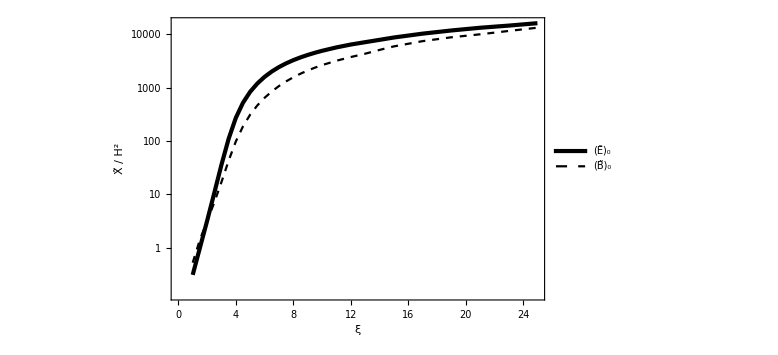

```mathematica
ListLogPlot[{consistentE0,consistentB0},FrameLabel->{ξ,Row[{OverTilde[X]," / ",H^2}]},PlotLegends->Placed[{Subscript[OverTilde["E"], 0],Subscript[OverTilde[B], 0]},{0.8,0.2}],PlotStyle->{{AbsoluteThickness[3],Black},{Black,Dashed}}]
```

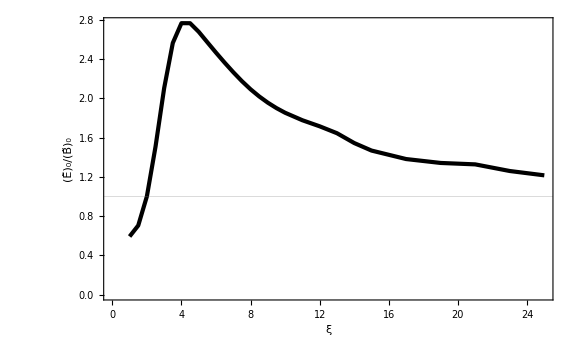

```mathematica
ListPlot[E0oB0,PlotStyle->{AbsoluteThickness[3],Black},GridLines->{None,{1}},FrameLabel->{ξ,Row[{Subscript[OverTilde["E"], 0],"/",Subscript[OverTilde[B], 0]}]}]
```

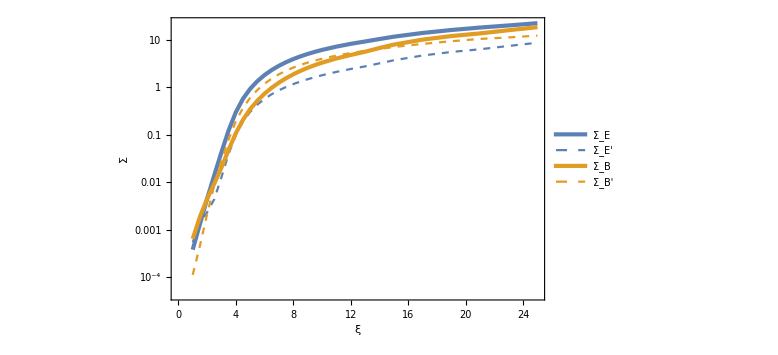

```mathematica
ListLogPlot[{consistentSgE,consistentSgEp,consistentSgB,consistentSgBp},FrameLabel->{ξ,Σ},PlotLegends->Placed[LineLegend[{Subscript[Σ, "E"],Subscript[Σ, "E"'],Subscript[Σ, B],Subscript[Σ, B']},LegendLayout->"Row",LegendMarkerSize->20],{0.65,0.15}],PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},{Color[2],AbsoluteThickness[3]},{Color[2],Dashed}}]
```

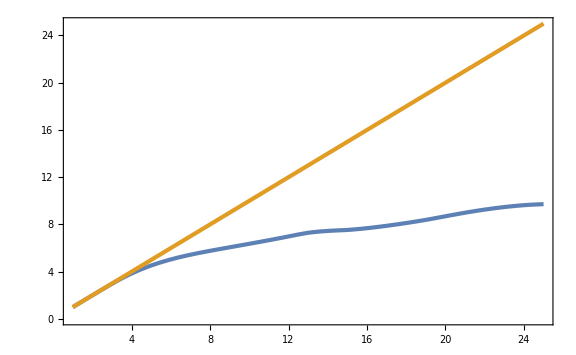

```mathematica
Plot[{xi-(SgBint[xi]+SgBpint[xi])/2,xi},{xi,1,25}]
```

```mathematica
power9List=Sort[Import["c++/power_9.dat"]];
power19List=Sort[Import["c++/power_19.dat"]];
pmax9List=Sort[Import["c++/power_max_9.dat"]];
pmax19List=Sort[Import["c++/power_max_19.dat"]];
```

```mathematica
PEE9List=Table[{power9List[[i,1]],power9List[[i,2]],power9List[[i,3]]},{i,Length[power9List]}];
PBB9List=Table[{power9List[[i,1]],power9List[[i,2]],power9List[[i,4]]},{i,Length[power9List]}];
PEE19List=Table[{power19List[[i,1]],power19List[[i,2]],power19List[[i,3]]},{i,Length[power19List]}];
PBB19List=Table[{power19List[[i,1]],power19List[[i,2]],power19List[[i,4]]},{i,Length[power19List]}];
PEEmax9List=Table[{pmax9List[[i,1]],pmax9List[[i,2]]},{i,Length[pmax9List]}];
PBBmax9List=Table[{pmax9List[[i,1]],pmax9List[[i,3]]},{i,Length[pmax9List]}];
normPEE9List=Table[{pmax9List[[i,1]],pmax9List[[i,2]]/Last[pmax9List][[2]]},{i,Length[pmax9List]}];
normPBB9List=Table[{pmax9List[[i,1]],pmax9List[[i,3]]/Last[pmax9List][[3]]},{i,Length[pmax9List]}];normPEE19List=Table[{pmax19List[[i,1]],pmax19List[[i,2]]/Last[pmax19List][[2]]},{i,Length[pmax19List]}];
normPBB19List=Table[{pmax19List[[i,1]],pmax19List[[i,3]]/Last[pmax19List][[3]]},{i,Length[pmax19List]}];
```

```mathematica
PEE9int[cs_,x_]=Interpolation[PEE9List][cs,x];
PBB9int[cs_,x_]=Interpolation[PBB9List][cs,x];
PEE19int[cs_,x_]=Interpolation[PEE19List][cs,x];
PBB19int[cs_,x_]=Interpolation[PBB19List][cs,x];
```

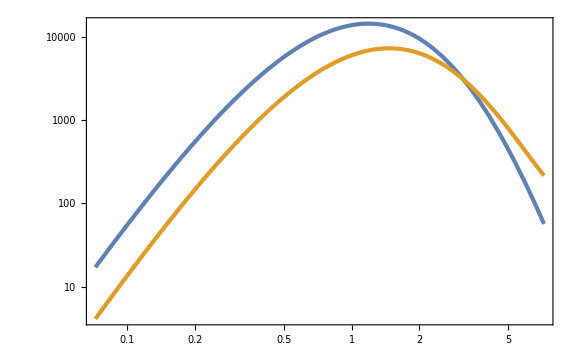

```mathematica
LogLogPlot[{PEE9int[0.5,x],PBB9int[0.5,x]},{x,10^-2 9 0.8, 9 0.8}]
```

```mathematica
Manipulate[LogLogPlot[{PEE19int[cs,x]/Last[pmax19List][[2]],PBB19int[cs,x]/Last[pmax19List][[3]]},{x,10^-2 19 0.8,19 0.8},PlotRange->{10^-18,10},FrameLabel->{{Row[{(Subscript[OverTilde[𝒫], X]^σ)[Subscript[θ, k]]," / ",(Subscript[OverTilde[𝒫], X]^σ)[0]}],None},{z,Row[{ξ==19,",  ",Cos[Subscript[θ, k]]==cs}]}},PlotLegends->Placed[LineLegend[{"E",B},LegendLayout->"Row"],{0.6,0.1}]],{cs,0,1,0.01}]
```

```mathematica
FigPList=Table[LogLogPlot[{PEE19int[cs,x]/Last[pmax19List][[2]],PBB19int[cs,x]/Last[pmax19List][[3]]},{x,10^-2 19 0.8,19 0.8},PlotRange->{10^-18,10},FrameLabel->{{Row[{(Subscript[OverTilde[𝒫], X]^σ)[Subscript[θ, k]]," / ",(Subscript[OverTilde[𝒫], X]^σ)[0]}],None},{z,Row[{ξ==19,",  ",Cos[Subscript[θ, k]]==cs}]}},PlotLegends->Placed[LineLegend[{"E",B},LegendLayout->"Row"],{0.6,0.1}]],{cs,0,1,0.01}];
```

```mathematica
Export["Pzcos.gif",FigPList];
```

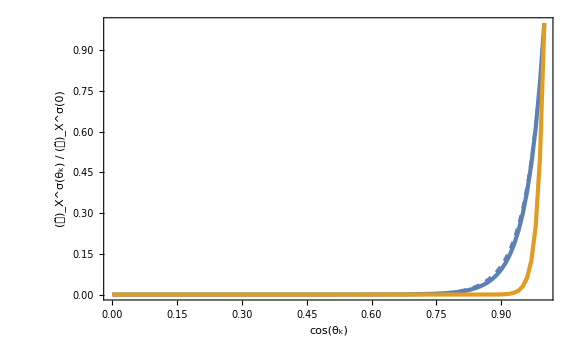

```mathematica
ListPlot[{normPEE9List,normPBB9List,normPEE19List,normPBB19List},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},{AbsoluteThickness[3],Color[2]},{Color[2],Dashed},{AbsoluteThickness[3],Color[3]},{Color[3],Dashed}},PlotRange->Full,FrameLabel->{Cos[Subscript[θ, k]],Row[{(Subscript[OverTilde[𝒫], X]^σ)[Subscript[θ, k]]," / ",(Subscript[OverTilde[𝒫], X]^σ)[0]}]}]
```

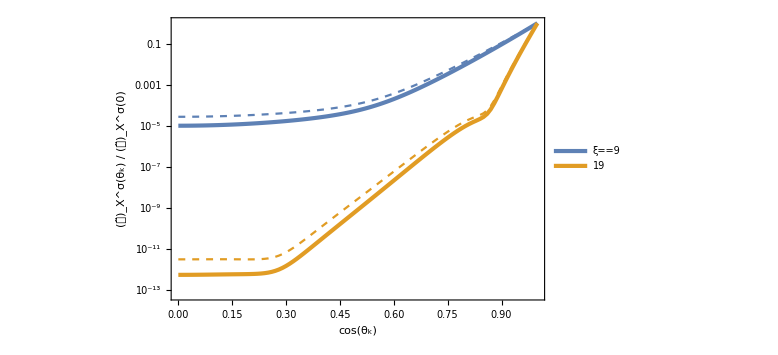

```mathematica
ListLogPlot[{normPEE9List,normPBB9List,normPEE19List,normPBB19List},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},{AbsoluteThickness[3],Color[2]},{Color[2],Dashed},{AbsoluteThickness[3],Color[3]},{Color[3],Dashed}},PlotRange->Full,FrameLabel->{Cos[Subscript[θ, k]],Row[{(Subscript[OverTilde[𝒫], X]^σ)[Subscript[θ, k]]," / ",(Subscript[OverTilde[𝒫], X]^σ)[0]}]},PlotLegends->Placed[{ξ==9,None,19,None},{0.8,0.2}]]
```